```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\PC\Documents\GitHub\QMLTests\IrisDS

```mathematica
nnoise=Import["feature_nnoise.csv"];
```

```mathematica
noise=Import["feature_noise.csv"];
```

```mathematica
x=noise[[2;;,1]];
y=nnoise[[2;;,1]];
```

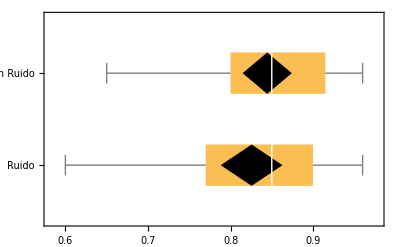

```mathematica
graf=BoxWhiskerChart[{x,y},{"Diamond",{"MeanDiamond",1,Black}},BarOrigin->Right,ChartLabels->{"Ruido","Sin Ruido"},ScalingFunctions->"Reverse"]
```

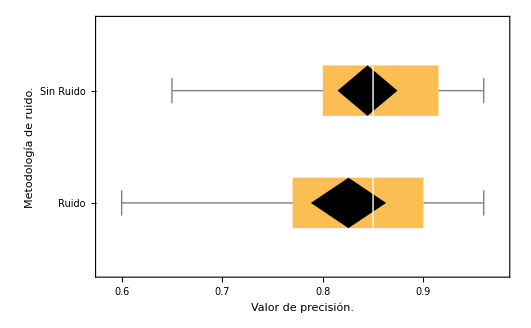

```mathematica
Show[graf,FrameLabel->{{RawBoxes[RowBox[{"Metodología"," ","de"," ",RowBox[{"ruido","."}]}]],None},{RawBoxes[RowBox[{"Valor"," ","de"," ",RowBox[{"precisión","."}]}]],HoldForm[Distribución de la ejecución VQC FeatureMap]}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Mean[x]
```

0.825556

```mathematica
With[
{α=0.05,x=noise[[2;;,1]],
y=nnoise[[2;;,1]]},
KolmogorovSmirnovTest[x,y,"TestDataTable", SignificanceLevel->α]]
```

| Statistic | P-Value
Kolmogorov-Smirnov | 0.148148 | 0.746643